```mathematica
SymbolToSets[v1ex25adx368bx479c]
```

{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9,12}}

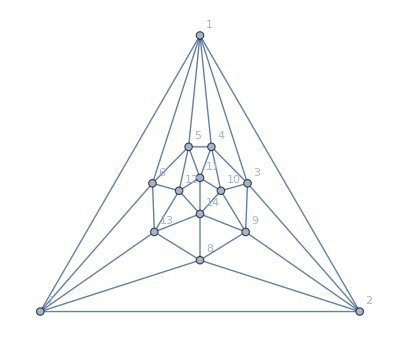

```mathematica
pl1=Graph[plantri[[2]],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
ffpl1=FindFullFormula[pl1];
```

```mathematica
Select[VertexList[pl1],VertexDegree[pl1,#]==5&]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
pl1gen=Select[ffpl1,StringCount[SymbolName[#],"x"]==3&]
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b}

```mathematica
Investigate3[all_]:=Block[{two,three,four,five, solthree, solfour, solfive,soltwo,reptwo,  repthree,repfour,repfive,result={}},
Table[
result=DeleteDuplicates[Join[result,DirectRefinements[set]]];
,
{set, all}
];
Table[
four=Map[NotThis[#,4]&,sets];
four[[4]]=Append[four[[4]],4];

five=Map[NotThis[#,5]&,sets];
five[[4]]=Append[five[[4]],5];


two=Map[NotThis[#,2]&,sets];
two[[4]]=Append[two[[4]],2];


three=Map[NotThis[#,3]&,sets];
three[[4]]=Append[three[[4]],3];

soltwo=DirectRefinements[two];
solthree=DirectRefinements[three];
solfour=DirectRefinements[four];
solfive=DirectRefinements[five];
reptwo=Table[k->Style[k,Italic],{k,soltwo}];
repthree=Table[k->Style[k,Underlined],{k,solthree}];
repfour=Table[k->Style[k,Green],{k,solfour}];
repfive=Table[k->Style[k,Bold],{k,solfive}];
result=(((result/.reptwo)/.repthree)/.repfour)/.repfive
,
{sets,  all }
]
]
```

```mathematica
Investigate3[Map[SymbolToSets[#]&,pl1gen]]
```

{{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{13}},{{1,13},{2,6,10},{3,5,7,14},{4,8,12},{9,11}},{{1,9,13},{2,6,10},{3,5,7,14},{4,8,12},{11}},{{1,11},{2,6,10},{3,5,7,14},{4,8,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,8,12},{6,10}},{{1,9,11,13},{2,6},{3,5,7,14},{4,8,12},{10}},{{1,9,11,13},{2,10},{3,5,7,14},{4,8,12},{6}},{{1,9,11,13},{2,6,10},{3},{4,8,12},{5,7,14}},{{1,9,11,13},{2,6,10},{3,5},{4,8,12},{7,14}},{{1,9,11,13},{2,6,10},{3,7,14},{4,8,12},{5}},{{1,9,11,13},{2,6,10},{3,5,7},{4,8,12},{14}},{{1,9,11,13},{2,6,10},{3,14},{4,8,12},{5,7}},{{1,9,11,13},{2,6,10},{3,5,14},{4,8,12},{7}},{{1,9,11,13},{2,6,10},{3,7},{4,8,12},{5,14}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4},{8,12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,8},{12}},{{1,9,11,13},{2,6,10},{3,5,7,14},{4,12},{8}},{{1},{2,5,10,13},{3,6,8,11},{4,7,14},{9,12}},{{1,9},{2,5,10,13},{3,6,8,11},{4,7,14},{12}},{{1,12},{2,5,10,13},{3,6,8,11},{4,7,14},{9}},{{1,9,12},{2},{3,6,8,11},{4,7,14},{5,10,13}},{{1,9,12},{2,5},{3,6,8,11},{4,7,14},{10,13}},{{1,9,12},{2,10,13},{3,6,8,11},{4,7,14},{5}},{{1,9,12},{2,5,10},{3,6,8,11},{4,7,14},{13}},{{1,9,12},{2,13},{3,6,8,11},{4,7,14},{5,10}},{{1,9,12},{2,5,13},{3,6,8,11},{4,7,14},{10}},{{1,9,12},{2,10},{3,6,8,11},{4,7,14},{5,13}},{{1,9,12},{2,5,10,13},{3},{4,7,14},{6,8,11}},{{1,9,12},{2,5,10,13},{3,6},{4,7,14},{8,11}},{{1,9,12},{2,5,10,13},{3,8,11},{4,7,14},{6}},{{1,9,12},{2,5,10,13},{3,6,8},{4,7,14},{11}},{{1,9,12},{2,5,10,13},{3,11},{4,7,14},{6,8}},{{1,9,12},{2,5,10,13},{3,6,11},{4,7,14},{8}},{{1,9,12},{2,5,10,13},{3,8},{4,7,14},{6,11}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4},{7,14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,7},{14}},{{1,9,12},{2,5,10,13},{3,6,8,11},{4,14},{7}},{{1},{2,4,6,14},{3,8,12},{5,7,10},{9,11,13}},{{1,9},{2,4,6,14},{3,8,12},{5,7,10},{11,13}},{{1,11,13},{2,4,6,14},{3,8,12},{5,7,10},{9}},{{1,9,11},{2,4,6,14},{3,8,12},{5,7,10},{13}},{{1,13},{2,4,6,14},{3,8,12},{5,7,10},{9,11}},{{1,9,13},{2,4,6,14},{3,8,12},{5,7,10},{11}},{{1,11},{2,4,6,14},{3,8,12},{5,7,10},{9,13}},{{1,9,11,13},{2},{3,8,12},{4,6,14},{5,7,10}},{{1,9,11,13},{2,4},{3,8,12},{5,7,10},{6,14}},{{1,9,11,13},{2,6,14},{3,8,12},{4},{5,7,10}},{{1,9,11,13},{2,4,6},{3,8,12},{5,7,10},{14}},{{1,9,11,13},{2,14},{3,8,12},{4,6},{5,7,10}},{{1,9,11,13},{2,4,14},{3,8,12},{5,7,10},{6}},{{1,9,11,13},{2,6},{3,8,12},{4,14},{5,7,10}},{{1,9,11,13},{2,4,6,14},{3},{5,7,10},{8,12}},{{1,9,11,13},{2,4,6,14},{3,8},{5,7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,7,10},{8}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5},{7,10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,7},{10}},{{1,9,11,13},{2,4,6,14},{3,8,12},{5,10},{7}},{{1},{2,4,6,14},{3,7,12},{5,8,10},{9,11,13}},{{1,9},{2,4,6,14},{3,7,12},{5,8,10},{11,13}},{{1,11,13},{2,4,6,14},{3,7,12},{5,8,10},{9}},{{1,9,11},{2,4,6,14},{3,7,12},{5,8,10},{13}},{{1,13},{2,4,6,14},{3,7,12},{5,8,10},{9,11}},{{1,9,13},{2,4,6,14},{3,7,12},{5,8,10},{11}},{{1,11},{2,4,6,14},{3,7,12},{5,8,10},{9,13}},{{1,9,11,13},{2},{3,7,12},{4,6,14},{5,8,10}},{{1,9,11,13},{2,4},{3,7,12},{5,8,10},{6,14}},{{1,9,11,13},{2,6,14},{3,7,12},{4},{5,8,10}},{{1,9,11,13},{2,4,6},{3,7,12},{5,8,10},{14}},{{1,9,11,13},{2,14},{3,7,12},{4,6},{5,8,10}},{{1,9,11,13},{2,4,14},{3,7,12},{5,8,10},{6}},{{1,9,11,13},{2,6},{3,7,12},{4,14},{5,8,10}},{{1,9,11,13},{2,4,6,14},{3},{5,8,10},{7,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5,8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,12},{5,8,10},{7}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5},{8,10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,8},{10}},{{1,9,11,13},{2,4,6,14},{3,7,12},{5,10},{8}},{{1},{2,4,6},{3,5,7,14},{8,10,12},{9,11,13}},{{1,9},{2,4,6},{3,5,7,14},{8,10,12},{11,13}},{{1,11,13},{2,4,6},{3,5,7,14},{8,10,12},{9}},{{1,9,11},{2,4,6},{3,5,7,14},{8,10,12},{13}},{{1,13},{2,4,6},{3,5,7,14},{8,10,12},{9,11}},{{1,9,13},{2,4,6},{3,5,7,14},{8,10,12},{11}},{{1,11},{2,4,6},{3,5,7,14},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7,14},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7,14},{4},{8,10,12}},{{1,9,11,13},{2,4,6},{3},{5,7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5},{7,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7,14},{5},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7},{8,10,12},{14}},{{1,9,11,13},{2,4,6},{3,14},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,14},{7},{8,10,12}},{{1,9,11,13},{2,4,6},{3,7},{5,14},{8,10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8},{10,12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,10},{12}},{{1,9,11,13},{2,4,6},{3,5,7,14},{8,12},{10}},{{1},{2,4,6,14},{3,5,7},{8,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,7},{8,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,7},{8,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,7},{8,10,12},{13}},{{1,13},{2,4,6,14},{3,5,7},{8,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,7},{8,10,12},{11}},{{1,11},{2,4,6,14},{3,5,7},{8,10,12},{9,13}},{{1,9,11,13},{2},{3,5,7},{4,6,14},{8,10,12}},{{1,9,11,13},{2,4},{3,5,7},{6,14},{8,10,12}},{{1,9,11,13},{2,6,14},{3,5,7},{4},{8,10,12}},{{1,9,11,13},{2,14},{3,5,7},{4,6},{8,10,12}},{{1,9,11,13},{2,4,14},{3,5,7},{6},{8,10,12}},{{1,9,11,13},{2,6},{3,5,7},{4,14},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,7},{5},{8,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,7},{8,12},{10}},{{1},{2,4,6,14},{3,5,8},{7,10,12},{9,11,13}},{{1,9},{2,4,6,14},{3,5,8},{7,10,12},{11,13}},{{1,11,13},{2,4,6,14},{3,5,8},{7,10,12},{9}},{{1,9,11},{2,4,6,14},{3,5,8},{7,10,12},{13}},{{1,13},{2,4,6,14},{3,5,8},{7,10,12},{9,11}},{{1,9,13},{2,4,6,14},{3,5,8},{7,10,12},{11}},{{1,11},{2,4,6,14},{3,5,8},{7,10,12},{9,13}},{{1,9,11,13},{2},{3,5,8},{4,6,14},{7,10,12}},{{1,9,11,13},{2,4},{3,5,8},{6,14},{7,10,12}},{{1,9,11,13},{2,6,14},{3,5,8},{4},{7,10,12}},{{1,9,11,13},{2,4,6},{3,5,8},{7,10,12},{14}},{{1,9,11,13},{2,14},{3,5,8},{4,6},{7,10,12}},{{1,9,11,13},{2,4,14},{3,5,8},{6},{7,10,12}},{{1,9,11,13},{2,6},{3,5,8},{4,14},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3},{5,8},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5},{7,10,12},{8}},{{1,9,11,13},{2,4,6,14},{3,8},{5},{7,10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7},{10,12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,10},{12}},{{1,9,11,13},{2,4,6,14},{3,5,8},{7,12},{10}},{{1},{2,4,12},{3,5,7,14},{6,8,10},{9,11,13}},{{1,9},{2,4,12},{3,5,7,14},{6,8,10},{11,13}},{{1,11,13},{2,4,12},{3,5,7,14},{6,8,10},{9}},{{1,9,11},{2,4,12},{3,5,7,14},{6,8,10},{13}},{{1,13},{2,4,12},{3,5,7,14},{6,8,10},{9,11}},{{1,9,13},{2,4,12},{3,5,7,14},{6,8,10},{11}},{{1,11},{2,4,12},{3,5,7,14},{6,8,10},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,12},{6,8,10}},{{1,9,11,13},{2,4},{3,5,7,14},{6,8,10},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4},{6,8,10}},{{1,9,11,13},{2,4,12},{3},{5,7,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5},{6,8,10},{7,14}},{{1,9,11,13},{2,4,12},{3,7,14},{5},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7},{6,8,10},{14}},{{1,9,11,13},{2,4,12},{3,14},{5,7},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,14},{6,8,10},{7}},{{1,9,11,13},{2,4,12},{3,7},{5,14},{6,8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6},{8,10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,8},{10}},{{1,9,11,13},{2,4,12},{3,5,7,14},{6,10},{8}},{{1},{2,11,13},{3,5,7,14},{4,6,9},{8,10,12}},{{1,8},{2,11,13},{3,5,7,14},{4,6,9},{10,12}},{{1,10,12},{2,11,13},{3,5,7,14},{4,6,9},{8}},{{1,8,10},{2,11,13},{3,5,7,14},{4,6,9},{12}},{{1,12},{2,11,13},{3,5,7,14},{4,6,9},{8,10}},{{1,8,12},{2,11,13},{3,5,7,14},{4,6,9},{10}},{{1,10},{2,11,13},{3,5,7,14},{4,6,9},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,6,9},{11,13}},{{1,8,10,12},{2,11},{3,5,7,14},{4,6,9},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4,6,9},{11}},{{1,8,10,12},{2,11,13},{3},{4,6,9},{5,7,14}},{{1,8,10,12},{2,11,13},{3,5},{4,6,9},{7,14}},{{1,8,10,12},{2,11,13},{3,7,14},{4,6,9},{5}},{{1,8,10,12},{2,11,13},{3,5,7},{4,6,9},{14}},{{1,8,10,12},{2,11,13},{3,14},{4,6,9},{5,7}},{{1,8,10,12},{2,11,13},{3,5,14},{4,6,9},{7}},{{1,8,10,12},{2,11,13},{3,7},{4,6,9},{5,14}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4},{6,9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,6},{9}},{{1,8,10,12},{2,11,13},{3,5,7,14},{4,9},{6}},{{1},{2,6,11},{3,5,7,14},{4,9,13},{8,10,12}},{{1,8},{2,6,11},{3,5,7,14},{4,9,13},{10,12}},{{1,10,12},{2,6,11},{3,5,7,14},{4,9,13},{8}},{{1,8,10},{2,6,11},{3,5,7,14},{4,9,13},{12}},{{1,12},{2,6,11},{3,5,7,14},{4,9,13},{8,10}},{{1,8,12},{2,6,11},{3,5,7,14},{4,9,13},{10}},{{1,10},{2,6,11},{3,5,7,14},{4,9,13},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,9,13},{6,11}},{{1,8,10,12},{2,6},{3,5,7,14},{4,9,13},{11}},{{1,8,10,12},{2,11},{3,5,7,14},{4,9,13},{6}},{{1,8,10,12},{2,6,11},{3},{4,9,13},{5,7,14}},{{1,8,10,12},{2,6,11},{3,5},{4,9,13},{7,14}},{{1,8,10,12},{2,6,11},{3,7,14},{4,9,13},{5}},{{1,8,10,12},{2,6,11},{3,5,7},{4,9,13},{14}},{{1,8,10,12},{2,6,11},{3,14},{4,9,13},{5,7}},{{1,8,10,12},{2,6,11},{3,5,14},{4,9,13},{7}},{{1,8,10,12},{2,6,11},{3,7},{4,9,13},{5,14}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4},{9,13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,9},{13}},{{1,8,10,12},{2,6,11},{3,5,7,14},{4,13},{9}},{{1},{2,5,10,13},{3,6,14},{4,7,9,12},{8,11}},{{1,8},{2,5,10,13},{3,6,14},{4,7,9,12},{11}},{{1,11},{2,5,10,13},{3,6,14},{4,7,9,12},{8}},{{1,8,11},{2},{3,6,14},{4,7,9,12},{5,10,13}},{{1,8,11},{2,5},{3,6,14},{4,7,9,12},{10,13}},{{1,8,11},{2,10,13},{3,6,14},{4,7,9,12},{5}},{{1,8,11},{2,5,10},{3,6,14},{4,7,9,12},{13}},{{1,8,11},{2,13},{3,6,14},{4,7,9,12},{5,10}},{{1,8,11},{2,5,13},{3,6,14},{4,7,9,12},{10}},{{1,8,11},{2,10},{3,6,14},{4,7,9,12},{5,13}},{{1,8,11},{2,5,10,13},{3},{4,7,9,12},{6,14}},{{1,8,11},{2,5,10,13},{3,6},{4,7,9,12},{14}},{{1,8,11},{2,5,10,13},{3,14},{4,7,9,12},{6}},{{1,8,11},{2,5,10,13},{3,6,14},{4},{7,9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7},{9,12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9,12},{7}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,9},{12}},{{1,8,11},{2,5,10,13},{3,6,14},{4,12},{7,9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,7,12},{9}},{{1,8,11},{2,5,10,13},{3,6,14},{4,9},{7,12}},{{1},{2,4,6,14},{3,11,13},{5,7,9},{8,10,12}},{{1,8},{2,4,6,14},{3,11,13},{5,7,9},{10,12}},{{1,10,12},{2,4,6,14},{3,11,13},{5,7,9},{8}},{{1,8,10},{2,4,6,14},{3,11,13},{5,7,9},{12}},{{1,12},{2,4,6,14},{3,11,13},{5,7,9},{8,10}},{{1,8,12},{2,4,6,14},{3,11,13},{5,7,9},{10}},{{1,10},{2,4,6,14},{3,11,13},{5,7,9},{8,12}},{{1,8,10,12},{2},{3,11,13},{4,6,14},{5,7,9}},{{1,8,10,12},{2,4},{3,11,13},{5,7,9},{6,14}},{{1,8,10,12},{2,6,14},{3,11,13},{4},{5,7,9}},{{1,8,10,12},{2,4,6},{3,11,13},{5,7,9},{14}},{{1,8,10,12},{2,14},{3,11,13},{4,6},{5,7,9}},{{1,8,10,12},{2,4,14},{3,11,13},{5,7,9},{6}},{{1,8,10,12},{2,6},{3,11,13},{4,14},{5,7,9}},{{1,8,10,12},{2,4,6,14},{3},{5,7,9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,11},{5,7,9},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5,7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5},{7,9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,7},{9}},{{1,8,10,12},{2,4,6,14},{3,11,13},{5,9},{7}},{{1},{2,4,6,14},{3,7,11},{5,9,13},{8,10,12}},{{1,8},{2,4,6,14},{3,7,11},{5,9,13},{10,12}},{{1,10,12},{2,4,6,14},{3,7,11},{5,9,13},{8}},{{1,8,10},{2,4,6,14},{3,7,11},{5,9,13},{12}},{{1,12},{2,4,6,14},{3,7,11},{5,9,13},{8,10}},{{1,8,12},{2,4,6,14},{3,7,11},{5,9,13},{10}},{{1,10},{2,4,6,14},{3,7,11},{5,9,13},{8,12}},{{1,8,10,12},{2},{3,7,11},{4,6,14},{5,9,13}},{{1,8,10,12},{2,4},{3,7,11},{5,9,13},{6,14}},{{1,8,10,12},{2,6,14},{3,7,11},{4},{5,9,13}},{{1,8,10,12},{2,4,6},{3,7,11},{5,9,13},{14}},{{1,8,10,12},{2,14},{3,7,11},{4,6},{5,9,13}},{{1,8,10,12},{2,4,14},{3,7,11},{5,9,13},{6}},{{1,8,10,12},{2,6},{3,7,11},{4,14},{5,9,13}},{{1,8,10,12},{2,4,6,14},{3},{5,9,13},{7,11}},{{1,8,10,12},{2,4,6,14},{3,7},{5,9,13},{11}},{{1,8,10,12},{2,4,6,14},{3,11},{5,9,13},{7}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5},{9,13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,9},{13}},{{1,8,10,12},{2,4,6,14},{3,7,11},{5,13},{9}},{{1,8},{2,4,6},{3,5,7,14},{9,11,13},{10,12}},{{1,10,12},{2,4,6},{3,5,7,14},{8},{9,11,13}},{{1,8,10},{2,4,6},{3,5,7,14},{9,11,13},{12}},{{1,12},{2,4,6},{3,5,7,14},{8,10},{9,11,13}},{{1,8,12},{2,4,6},{3,5,7,14},{9,11,13},{10}},{{1,10},{2,4,6},{3,5,7,14},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7,14},{4,6},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7,14},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7,14},{4},{9,11,13}},{{1,8,10,12},{2,4,6},{3},{5,7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5},{7,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7,14},{5},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7},{9,11,13},{14}},{{1,8,10,12},{2,4,6},{3,14},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,14},{7},{9,11,13}},{{1,8,10,12},{2,4,6},{3,7},{5,14},{9,11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9},{11,13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,11},{13}},{{1,8,10,12},{2,4,6},{3,5,7,14},{9,13},{11}},{{1,8},{2,4,6,14},{3,5,7},{9,11,13},{10,12}},{{1,10,12},{2,4,6,14},{3,5,7},{8},{9,11,13}},{{1,8,10},{2,4,6,14},{3,5,7},{9,11,13},{12}},{{1,12},{2,4,6,14},{3,5,7},{8,10},{9,11,13}},{{1,8,12},{2,4,6,14},{3,5,7},{9,11,13},{10}},{{1,10},{2,4,6,14},{3,5,7},{8,12},{9,11,13}},{{1,8,10,12},{2},{3,5,7},{4,6,14},{9,11,13}},{{1,8,10,12},{2,4},{3,5,7},{6,14},{9,11,13}},{{1,8,10,12},{2,6,14},{3,5,7},{4},{9,11,13}},{{1,8,10,12},{2,14},{3,5,7},{4,6},{9,11,13}},{{1,8,10,12},{2,4,14},{3,5,7},{6},{9,11,13}},{{1,8,10,12},{2,6},{3,5,7},{4,14},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3},{5,7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5},{7},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,7},{5},{9,11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9},{11,13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,5,7},{9,13},{11}},{{1},{2,4,6,14},{3,5,13},{7,9,11},{8,10,12}},{{1,8},{2,4,6,14},{3,5,13},{7,9,11},{10,12}},{{1,10,12},{2,4,6,14},{3,5,13},{7,9,11},{8}},{{1,8,10},{2,4,6,14},{3,5,13},{7,9,11},{12}},{{1,12},{2,4,6,14},{3,5,13},{7,9,11},{8,10}},{{1,8,12},{2,4,6,14},{3,5,13},{7,9,11},{10}},{{1,10},{2,4,6,14},{3,5,13},{7,9,11},{8,12}},{{1,8,10,12},{2},{3,5,13},{4,6,14},{7,9,11}},{{1,8,10,12},{2,4},{3,5,13},{6,14},{7,9,11}},{{1,8,10,12},{2,6,14},{3,5,13},{4},{7,9,11}},{{1,8,10,12},{2,4,6},{3,5,13},{7,9,11},{14}},{{1,8,10,12},{2,14},{3,5,13},{4,6},{7,9,11}},{{1,8,10,12},{2,4,14},{3,5,13},{6},{7,9,11}},{{1,8,10,12},{2,6},{3,5,13},{4,14},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3},{5,13},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5},{7,9,11},{13}},{{1,8,10,12},{2,4,6,14},{3,13},{5},{7,9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7},{9,11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,9},{11}},{{1,8,10,12},{2,4,6,14},{3,5,13},{7,11},{9}},{{1},{2,4,13},{3,5,7,14},{6,9,11},{8,10,12}},{{1,8},{2,4,13},{3,5,7,14},{6,9,11},{10,12}},{{1,10,12},{2,4,13},{3,5,7,14},{6,9,11},{8}},{{1,8,10},{2,4,13},{3,5,7,14},{6,9,11},{12}},{{1,12},{2,4,13},{3,5,7,14},{6,9,11},{8,10}},{{1,8,12},{2,4,13},{3,5,7,14},{6,9,11},{10}},{{1,10},{2,4,13},{3,5,7,14},{6,9,11},{8,12}},{{1,8,10,12},{2},{3,5,7,14},{4,13},{6,9,11}},{{1,8,10,12},{2,4},{3,5,7,14},{6,9,11},{13}},{{1,8,10,12},{2,13},{3,5,7,14},{4},{6,9,11}},{{1,8,10,12},{2,4,13},{3},{5,7,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5},{6,9,11},{7,14}},{{1,8,10,12},{2,4,13},{3,7,14},{5},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7},{6,9,11},{14}},{{1,8,10,12},{2,4,13},{3,14},{5,7},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,14},{6,9,11},{7}},{{1,8,10,12},{2,4,13},{3,7},{5,14},{6,9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6},{9,11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,9},{11}},{{1,8,10,12},{2,4,13},{3,5,7,14},{6,11},{9}}},{{{1},{2,5,10,13},{3,6,8,11},{4,7,9,12},{14}},{{1,14},{2},{3,6,8,11},{4,7,9,12},{5,10,13}},{{1,14},{2,5},{3,6,8,11},{4,7,9,12},{10,13}},{{1,14},{2,10,13},{3,6,8,11},{4,7,9,12},{5}},{{1,14},{2,5,10},{3,6,8,11},{4,7,9,12},{13}},{{1,14},{2,13},{3,6,8,11},{4,7,9,12},{5,10}},{{1,14},{2,5,13},{3,6,8,11},{4,7,9,12},{10}},{{1,14},{2,10},{3,6,8,11},{4,7,9,12},{5,13}},{{1,14},{2,5,10,13},{3},{4,7,9,12},{6,8,11}},{{1,14},{2,5,10,13},{3,6},{4,7,9,12},{8,11}},{{1,14},{2,5,10,13},{3,8,11},{4,7,9,12},{6}},{{1,14},{2,5,10,13},{3,6,8},{4,7,9,12},{11}},{{1,14},{2,5,10,13},{3,11},{4,7,9,12},{6,8}},{{1,14},{2,5,10,13},{3,6,11},{4,7,9,12},{8}},{{1,14},{2,5,10,13},{3,8},{4,7,9,12},{6,11}},{{1,14},{2,5,10,13},{3,6,8,11},{4},{7,9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7},{9,12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9,12},{7}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,9},{12}},{{1,14},{2,5,10,13},{3,6,8,11},{4,12},{7,9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,7,12},{9}},{{1,14},{2,5,10,13},{3,6,8,11},{4,9},{7,12}},{{1},{2,5,14},{3,6,8,11},{4,7,9,12},{10,13}},{{1,10},{2,5,14},{3,6,8,11},{4,7,9,12},{13}},{{1,13},{2,5,14},{3,6,8,11},{4,7,9,12},{10}},{{1,10,13},{2},{3,6,8,11},{4,7,9,12},{5,14}},{{1,10,13},{2,5},{3,6,8,11},{4,7,9,12},{14}},{{1,10,13},{2,14},{3,6,8,11},{4,7,9,12},{5}},{{1,10,13},{2,5,14},{3},{4,7,9,12},{6,8,11}},{{1,10,13},{2,5,14},{3,6},{4,7,9,12},{8,11}},{{1,10,13},{2,5,14},{3,8,11},{4,7,9,12},{6}},{{1,10,13},{2,5,14},{3,6,8},{4,7,9,12},{11}},{{1,10,13},{2,5,14},{3,11},{4,7,9,12},{6,8}},{{1,10,13},{2,5,14},{3,6,11},{4,7,9,12},{8}},{{1,10,13},{2,5,14},{3,8},{4,7,9,12},{6,11}},{{1,10,13},{2,5,14},{3,6,8,11},{4},{7,9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7},{9,12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9,12},{7}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,9},{12}},{{1,10,13},{2,5,14},{3,6,8,11},{4,12},{7,9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,7,12},{9}},{{1,10,13},{2,5,14},{3,6,8,11},{4,9},{7,12}},{{1},{2,10,12},{3,5,7,14},{4,6,8},{9,11,13}},{{1,9},{2,10,12},{3,5,7,14},{4,6,8},{11,13}},{{1,11,13},{2,10,12},{3,5,7,14},{4,6,8},{9}},{{1,9,11},{2,10,12},{3,5,7,14},{4,6,8},{13}},{{1,13},{2,10,12},{3,5,7,14},{4,6,8},{9,11}},{{1,9,13},{2,10,12},{3,5,7,14},{4,6,8},{11}},{{1,11},{2,10,12},{3,5,7,14},{4,6,8},{9,13}},{{1,9,11,13},{2},{3,5,7,14},{4,6,8},{10,12}},{{1,9,11,13},{2,10},{3,5,7,14},{4,6,8},{12}},{{1,9,11,13},{2,12},{3,5,7,14},{4,6,8},{10}},{{1,9,11,13},{2,10,12},{3},{4,6,8},{5,7,14}},{{1,9,11,13},{2,10,12},{3,5},{4,6,8},{7,14}},{{1,9,11,13},{2,10,12},{3,7,14},{4,6,8},{5}},{{1,9,11,13},{2,10,12},{3,5,7},{4,6,8},{14}},{{1,9,11,13},{2,10,12},{3,14},{4,6,8},{5,7}},{{1,9,11,13},{2,10,12},{3,5,14},{4,6,8},{7}},{{1,9,11,13},{2,10,12},{3,7},{4,6,8},{5,14}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4},{6,8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,6},{8}},{{1,9,11,13},{2,10,12},{3,5,7,14},{4,8},{6}},{{1},{2,6,10},{3,5,7,14},{4,8,12},{9,11,13}},{{1,9},{2,6,10},{3,5,7,14},{4,8,12},{11,13}},{{1,11,13},{2,6,10},{3,5,7,14},{4,8,12},{9}},{{1,9,11},{2,6,10},{3,5,7,14},{4,8,12},{1